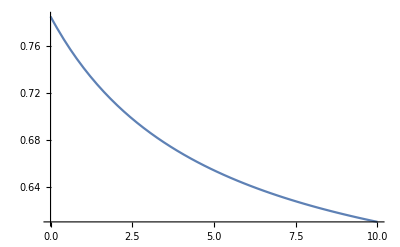

0.785398

```mathematica
Clear["Global`*"]
zetait[Rit_]:=ArcTan[(R0 Sin[zeta1]+Rit)/
			(R0 Cos[zeta1]+(Rit(Rlc/Tan[zeta]-R0 Cos[zeta1])/(Rlc - R0 Sin[zeta1])))];
Plot[zetait[Rit]/.{R0->10,zeta1->Pi/4,Rlc->10000.,zeta->Pi/6},{Rit,0,10}]
Pi/4.
```

```mathematica
rit[Rit_]:=Sqrt[(R0 Sin[zeta1]+Rit)^2 + (R0 Cos[zeta1]+Rit(Rlc/Tan[zeta]-R0 Cos[zeta1])/(Rlc-R0 Sin[zeta1]))^2];
Plot[rit[Rit]/.{R0->10,zeta1->Pi/4,Rlc->10000.,zeta->Pi/6},{Rit,0,11}]
rit[0]/.{R0->10,zeta1->Pi/4,Rlc->10000.,zeta->Pi/6}
10./Sin[Pi/4]
```

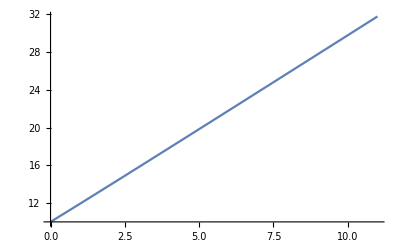

10

14.1421